```mathematica
dotset={{5,5060},{6,6528},{7,4587},{8,15309},{9,6678},{10,10234},{11,17853},{12,9107},{13,14902},{14,4338},{15,5073},{16,5784},{17,5987},{18,6706},{19,7054},{20,7243},{21,9154},{22,19119},{23,12133},{24,11780},{25,12784},{26,15303},{27,15254},{28,18988},{29,17169},{30,20964},{40,40963},{50,76573},{60,116608},{70,169819},{80,329900},{90,345886},{100,443440},{110,631416},{120,733760},{130,843051},{140,1013491},{150,1284146},{160,1420130},{170,1680586},{180,2014375},{190,2490014},{200,2711023}};
```

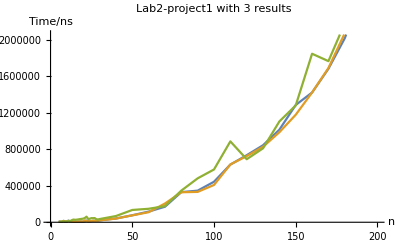

```mathematica
ListLinePlot[{dotset,dotset2,dotset3},PlotLabel->"Lab2-project1 with 3 results",AxesLabel->{"n","Time/ns"}]
```

```mathematica
dotset2={{5,6631},{6,5409},{7,6852},{8,14506},{9,9690},{10,7351},{11,13857},{12,8844},{13,4203},{14,6718},{15,4960},{16,5230},{17,8279},{18,9794},{19,8892},{20,7821},{21,20894},{22,13041},{23,9298},{24,11474},{25,13417},{26,17311},{27,15245},{28,16011},{29,16444},{30,20508},{40,40081},{50,75102},{60,109964},{70,204959},{80,328490},{90,332344},{100,408210},{110,632428},{120,724350},{130,826385},{140,985512},{150,1177012},{160,1420339},{170,1687920},{180,2069414},{190,2388714},{200,2583731}};
```

```mathematica
dotset3={{5,7050},{6,5893},{7,6304},{8,11489},{9,6931},{10,8199},{11,14817},{12,12017},{13,22142},{14,29534},{15,26511},{16,28277},{17,31082},{18,34280},{19,36829},{20,39459},{21,46584},{22,61240},{23,36441},{24,38158},{25,45095},{26,44689},{27,45512},{28,33679},{29,30066},{30,34783},{40,67928},{50,134390},{60,147441},{70,176560},{80,346302},{90,480752},{100,577739},{110,885312},{120,690031},{130,809434},{140,1103779},{150,1278728},{160,1844689},{170,1763695},{180,2177809},{190,2874320},{200,2756280}};
ListLinePlot[dotset3]
```

### ex2

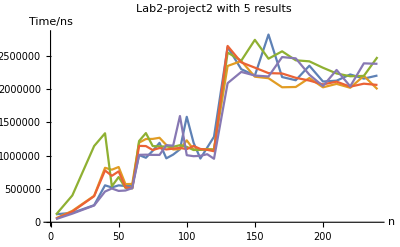

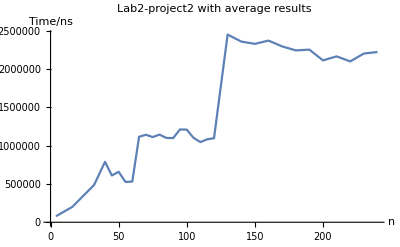

```mathematica
datasetex21={{4,120243},{16,141078},{32,256148},{40,554643},{45,522504},{50,554192},{55,543744},{60,548942},{65,1008757},{70,968789},{75,1072768},{80,1192777},{85,960137},{90,1016090},{95,1095136},{100,1584049},{105,1195222},{110,956975},{115,1121174},{120,1284300},{130,2631867},{140,2299319},{150,2204269},{160,2819435},{170,2181327},{180,2133098},{190,2351297},{200,2113902},{210,2126500},{220,2220130},{230,2157463},{240,2204128}};
datasetex22={{4,59003},{16,171231},{32,397276},{40,817666},{45,789488},{50,829626},{55,572934},{60,575427},{65,1195561},{70,1250125},{75,1251894},{80,1268791},{85,1160730},{90,1093340},{95,1098633},{100,1229768},{105,1094015},{110,1097454},{115,1098615},{120,1094512},{130,2347350},{140,2421873},{150,2186271},{160,2163535},{170,2027601},{180,2031821},{190,2166235},{200,2026743},{210,2078492},{220,2020372},{230,2199202},{240,1997824}};
datasetex23={{4,114929},{16,402838},{32,1144712},{40,1336512},{45,540312},{50,678859},{55,516381},{60,510308},{65,1219998},{70,1339201},{75,1144933},{80,1138713},{85,1138222},{90,1133375},{95,1157791},{100,1132112},{105,1084970},{110,1087169},{115,1091355},{120,1089521},{130,2548896},{140,2426648},{150,2739895},{160,2456636},{170,2567581},{180,2432678},{190,2416998},{200,2320709},{210,2234895},{220,2192934},{230,2198244},{240,2481468}};
datasetex24={{4,52348},{16,160237},{32,391259},{40,777961},{45,697502},{50,764420},{55,523880},{60,511473},{65,1147116},{70,1144383},{75,1084758},{80,1114922},{85,1093811},{90,1105832},{95,1116791},{100,1098632},{105,1146242},{110,1100817},{115,1088172},{120,1066574},{130,2648204},{140,2401869},{150,2322027},{160,2240142},{170,2234284},{180,2169880},{190,2128191},{200,2070407},{210,2112166},{220,2036477},{230,2081398},{240,2062339}};
datasetex25={{4,47497},{16,129115},{32,251808},{40,461269},{45,507047},{50,470727},{55,476569},{60,512723},{65,1012510},{70,1014706},{75,1011714},{80,1011774},{85,1157905},{90,1149821},{95,1595203},{100,1007325},{105,992245},{110,997730},{115,1022197},{120,953715},{130,2089102},{140,2258039},{150,2203884},{160,2189500},{170,2481138},{180,2461916},{190,2216488},{200,2045897},{210,2287614},{220,2041132},{230,2386812},{240,2379821}};
ListLinePlot[{datasetex21,datasetex22,datasetex23,datasetex24,datasetex25},PlotLabel->"Lab2-project2 with 5 results",AxesLabel->{"n","Time/ns"}]
ListLinePlot[Mean[{datasetex21,datasetex22,datasetex23,datasetex24,datasetex25}],PlotLabel->"Lab2-project2 with average results",AxesLabel->{"n","Time/ns"}]
```

```mathematica
Export["lab2-proj2-5.pdf",%41];
Export["lab2-proj2-average.pdf",%42];
Export["lab2-proj1-3.pdf",%46];
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["lab2-proj2-5.pdf"]]]
```

```mathematica
SystemOpen["lab2-proj2-average.pdf"]
```